```mathematica
Replace[f[100],x_->x+5]
```

5+f[100]

```mathematica
Replace[f[100],f[x_]->x+5]
```

105

```mathematica
f@{a,b,c,d}
```

f[{a,b,c,d}]

```mathematica
f/@{a,b,c,d}
```

{f[a],f[b],f[c],f[d]}

```mathematica
Nearest[{1,4,6,8,10,15}]
```

NearestFunction[…]

```mathematica
%[6.3]
```

{6}

```mathematica
%[7.8]
```

{6}[7.8]

```mathematica
Out[7][7.8]
```

{8}

```mathematica
Options[Framed]
```

{Alignment→Automatic,Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentPadding→True,DefaultBaseStyle→{},DefaultFrameStyle→{},FrameMargins→Automatic,FrameStyle→Automatic,ImageMargins→0,ImageSize→Automatic,RoundingRadius→0,StripOnInput→False}

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->(Hue[#3/3,.5]&)]
```

-Graphics3D-

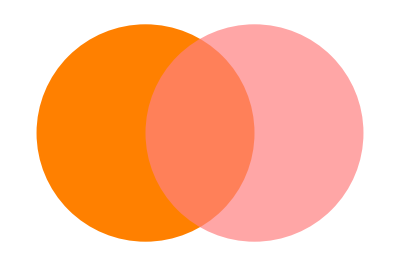

```mathematica
Graphics[{Orange,Disk[{0,0}],Opacity[.7],Pink,Disk[{1,0}]}]
```

```mathematica
Manipulate[Plot[Sin[a x],{x,0,10}],{a,1,5}]
```

```mathematica
Manipulate[Graphics3D[{EdgeForm[],(*No edges for the sphere surface*)(*Draw the sphere*){Opacity[0.6],Sphere[]},(*Draw meridian lines*)Table[Graphics3D[{Thick,Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]]}],{z,-1,1,0.2}]}],Boxed->False,(*Remove box around the plot*)SphericalRegion->True,(*Keep the sphere centered and unaffected by rotation*)(*Control the rotation of the sphere around the vertical axis*){angle,0,360},(*Angle in degrees*)(*Apply rotation to the entire sphere*)RotationTransform[angle Degree,{0,0,1}]]
```

Manipulate::vsform: Manipulate argument Boxed→False does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument SphericalRegion→True does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument RotationTransform[angle °,{0,0,1}] does not have the correct form for a variable specification.

General::stop: Further output of Manipulate::vsform will be suppressed during this calculation.

Manipulate[-Graphics3D-,Boxed→False,SphericalRegion→True,{angle,0,360},RotationTransform[angle °,{0,0,1}]]

```mathematica
Manipulate[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines*)Table[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],{z,-1,1,0.2}]},Boxed->False,(*Remove the box around the plot*)SphericalRegion->True (*Keep the sphere centered in the view*)],(*Control for rotation of the sphere around the vertical z-axis*){{angle,0,"Rotation Angle"},0,360},(*Rotation applied to the 3D graphics*)RotationAction->"Clip",Dynamic[RotationTransform[angle Degree,{0,0,1}]]]
```

Manipulate::vsform: Manipulate argument RotationAction→Clip does not have the correct form for a variable specification.

Manipulate[-Graphics3D-,{{angle,0,Rotation Angle},0,360},RotationAction→Clip,]

```mathematica
Manipulate[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines*)Table[Rotate[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],angle Degree,{0,0,1}],{z,-1,1,0.2}]},Boxed->False,(*Remove the box around the plot*)SphericalRegion->True (*Keep the sphere centered in the view*)],{{angle,0,"Rotation Angle"},0,360}]
```

```mathematica
Manipulate[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines*)Table[Rotate[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],{xRot Degree,yRot Degree,zRot Degree}],{z,-1,1,0.2}]},Boxed->True,(*Display the surrounding box*)SphericalRegion->True (*Keep the sphere centered in the view*)],{{xRot,0,"X Rotation"},0,360},{{yRot,0,"Y Rotation"},0,360},{{zRot,0,"Z Rotation"},0,360}]
```

```mathematica
Manipulate[Rotate[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines*)Table[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],{z,-1,1,0.2}]},Boxed->True,(*Display the surrounding box*)SphericalRegion->True (*Keep the sphere centered in the view*)],{xRot Degree,yRot Degree,zRot Degree} (*Apply rotation to entire Graphics3D object*)],{{xRot,0,"X Rotation"},0,360},{{yRot,0,"Y Rotation"},0,360},{{zRot,0,"Z Rotation"},0,360}]
```

```mathematica
Manipulate[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines on the sphere*)Table[Rotate[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],{xRot Degree,yRot Degree,zRot Degree}],{z,-1,1,0.2}],(*Draw a custom box to simulate the rotating box effect*)Rotate[{Line[{{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1},{-1,-1,-1}}],(*Bottom square*)Line[{{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1},{-1,-1,1}}],(*Top square*)Line[{{-1,-1,-1},{-1,-1,1}}],(*Vertical edges*)Line[{{1,-1,-1},{1,-1,1}}],Line[{{1,1,-1},{1,1,1}}],Line[{{-1,1,-1},{-1,1,1}}]},{xRot Degree,yRot Degree,zRot Degree}]},SphericalRegion->True],{{xRot,0,"X Rotation"},0,360},{{yRot,0,"Y Rotation"},0,360},{{zRot,0,"Z Rotation"},0,360}]
```

```mathematica
Manipulate[GeometricTransformation[Graphics3D[{Opacity[0.6],Sphere[],(*Draw the sphere with some transparency*)(*Draw meridian lines on the sphere*)Table[Line[Table[{Cos[θ],Sin[θ],z},{θ,0,2 π,π/36}]],{z,-1,1,0.2}],(*Draw a custom box to simulate the rotating box effect*)Line[{{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1},{-1,-1,-1}}],(*Bottom square*)Line[{{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1},{-1,-1,1}}],(*Top square*)Line[{{-1,-1,-1},{-1,-1,1}}],(*Vertical edges*)Line[{{1,-1,-1},{1,-1,1}}],Line[{{1,1,-1},{1,1,1}}],Line[{{-1,1,-1},{-1,1,1}}]},Boxed->False,(*Disable default box to avoid confusion with custom box*)SphericalRegion->True],(*Apply rotation to the entire Graphics3D object*)RotationTransform[{{1,0,0},{0,1,0},{0,0,1}}.RotationMatrix3D[xRot Degree,{1,0,0}].RotationMatrix3D[yRot Degree,{0,1,0}].RotationMatrix3D[zRot Degree,{0,0,1}}]
],{{xRot,0,"X Rotation"},0,360},{{yRot,0,"Y Rotation"},0,360},{{zRot,0,"Z Rotation"},0,360}
]
```

```mathematica
Manipulate[Graphics3D[GeometricTransformation[{(*Draw the sphere with latitude and longitude lines*)Opacity[0.6],(*Make the sphere semi-transparent*)Sphere[{0,0,0},(*Center of the sphere*)1,(*Radius of the sphere*)Mesh->{15,15},(*Number of latitude and longitude lines*)MeshStyle->Directive[Black,Thick] (*Style of the mesh lines*)]},(*Apply the rotation transformation*)rotationMatrix],Boxed->True,(*Show the bounding box*)SphericalRegion->True (*Keep the sphere centered in the view*)],{{xRot,0,"X Rotation"},0,360},(*Slider for x-axis rotation*){{yRot,0,"Y Rotation"},0,360},(*Slider for y-axis rotation*){{zRot,0,"Z Rotation"},0,360},(*Slider for z-axis rotation*)Dynamic[(*Calculate the combined rotation matrix*)rotationMatrix=RotationMatrix[zRot Degree,{0,0,1}].(*Rotate around z-axis*)RotationMatrix[yRot Degree,{0,1,0}].(*Rotate around y-axis*)RotationMatrix[xRot Degree,{1,0,0}]   (*Rotate around x-axis*)]]
```

```mathematica
Manipulate[Range[n],{n,3,10,1}]
```

```mathematica
eq=r==C/(2 Pi);
newEq=eq/. Pi->I Log[-1]
```

r==-C/(2 π)

```mathematica
(*Define the circumference C*)C=10; (*You can replace this with any value for C*)

(*Calculate r without using Pi by substituting Pi with I Log[-1]*)
r=C/(2*I*Log[-1])
```

Set::wrsym: Symbol C is Protected.

-C/(2 π)

```mathematica
(*Define the circumference C*)c=10; (*You can replace this with any value for C*)

(*Calculate r without using Pi by substituting Pi with I Log[-1]*)
r=c/(2*I*Log[-1])
```

-5/π

```mathematica
Manipulate[r=c/(2*I*Log[-1]),{{c,10,"Circumference (c)"},1,100}]
```

```mathematica
(*Define the expression for r in terms of C with the substitution for π*)r[c_]:=c/(2*I*Log[-1])

(*Plot the real and imaginary parts of r as C varies from 1 to 100*)
Plot[{Re[r[c]],Im[r[c]]},{c,1,100},PlotLabels->{"Real part of r","Imaginary part of r"},PlotStyle->{Blue,Dashed,Red},AxesLabel->{"Circumference (c)","Radius (r)"},PlotLegends->{"Real part of r","Imaginary part of r"},PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"]
```

SetDelayed::write: Tag Real in (-0.159155)[c_] is Protected.

$Failed

-Graphics-

```mathematica
(*Define the expression for r in terms of c with the substitution for π*)r[c_]:=c/(2*I*Log[-1])

(*Plot the real and imaginary parts of r as c varies from 1 to 100*)
Plot[{Re[r[c]],Im[r[c]]},{c,1,100},PlotLabels->{"Real part of r","Imaginary part of r"},PlotStyle->{Blue,Dashed,Red},AxesLabel->{"Circumference (c)","Radius (r)"},PlotLegends->{"Real part of r","Imaginary part of r"},PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"]
```

SetDelayed::write: Tag Real in (-0.159155)[c_] is Protected.

$Failed

-Graphics-

```mathematica
(*Define the expression for r in terms of c with the substitution for π*)r[c_]:=c/(2*I*Log[-1])

(*Plot the real and imaginary parts of r as c varies from 1 to 100*)
Plot[Evaluate[{Re[r[c]],Im[r[c]]}],{c,1,100},PlotLabels->{"Real part of r","Imaginary part of r"},PlotStyle->{Blue,Dashed,Red},AxesLabel->{"Circumference (c)","Radius (r)"},PlotLegends->{"Real part of r","Imaginary part of r"},PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"]
```

SetDelayed::write: Tag Real in (-0.159155)[c_] is Protected.

$Failed

-Graphics-

```mathematica
r[36]
```

(-0.159155)[36]

```mathematica
r[c_]:=c/(2*I*Log[-1])
```

SetDelayed::write: Tag Real in (-0.159155)[c_] is Protected.

$Failed

```mathematica
r[10]
```

(-0.159155)[10]

```mathematica
r[c_]:=c/(-2*Pi)
```

SetDelayed::write: Tag Real in (-0.159155)[c_] is Protected.

$Failed

```mathematica
r[10]
```

(-0.159155)[10]

```mathematica
Clear[r,c]
r[c_]:=c/(-2*Pi)
r[10]
```

-5/π

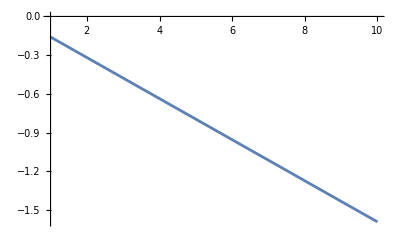

```mathematica
Plot[r[c],{c,1,10}]
```

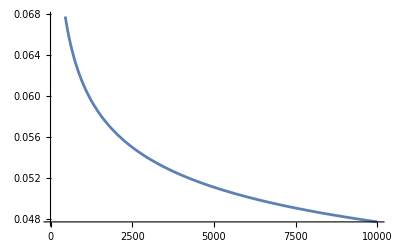

```mathematica
a[r_]:=1/Log[4*Pi*r^2]
Plot[{a[r]},{r,1,10000}]
```

```mathematica
(*Define the y-coordinate on the parabola as a function of x and focal length f*)y[x_,f_]:=x^2/(4*f)

(*Example:Calculate a point on the parabola for x=2 and focal length f=1*)
point={2,y[2,1]}
```

{2,1}

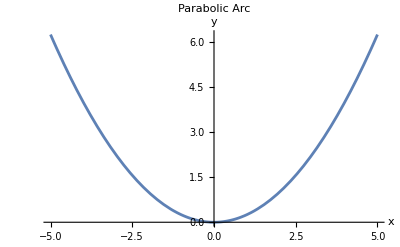

```mathematica
Plot[y[x,1],{x,-5,5},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Parabolic Arc"]
```

```mathematica
Manipulate[Plot[x^2/(4*f),{x,-5,5},PlotRange->{{-5,5},{0,10}},AxesLabel->{"x","y"},PlotLabel->"Parabolic Arc with Focal Length f"],{f,0.01,10}]
```

```mathematica
Manipulate[Plot[Evaluate[{Sqrt[(x^2/a^2-1)*b^2],-Sqrt[(x^2/a^2-1)*b^2]}],{x,-3 a,3 a},PlotRange->{{-3 a,3 a},{-3 b,3 b}},AxesLabel->{"x","y"},PlotLabels->{"Upper Branch","Lower Branch"},PlotStyle->{Blue,Red},PlotLegends->{"Upper Branch","Lower Branch"},PlotTheme->"Detailed",GridLines->Automatic],{{a,1,"a"},0.1,5},{{b,1,"b"},0.1,5}]
```

```mathematica
Manipulate[With[{b=Sqrt[c^2-a^2]},Plot[Evaluate[{Sqrt[(x^2/a^2-1)*b^2],-Sqrt[(x^2/a^2-1)*b^2]}],{x,-3 c,3 c},PlotRange->{{-3 c,3 c},{-3 b,3 b}},AxesLabel->{"x","y"},PlotLabels->{"Upper Branch","Lower Branch"},PlotStyle->{Blue,Red},PlotLegends->{"Upper Branch","Lower Branch"},PlotTheme->"Detailed",GridLines->Automatic]],{{a,1,"a"},0.1,5},{{c,2,"Focus Distance (c)"},0.1,10,Appearance->"Labeled",Enabled->Dynamic[c>=a]} (*ensures c>=a to avoid imaginary b*)]
```